```mathematica
f[x_]:=Factorial[x]
padeP[L_,M_,x_]:=Sum[f[(M+L-i)]/f[i]/f[L-i]*x^i,{i,0,L}]
padeQ[L_,M_,x_]:=f[M]/f[L]*Sum[f[(M+L-i)]/f[i]/f[M-i]*(-x)^i,{i,0,M}]
P[L_,M_,a_,x_]:=a*padeP[M,M,x]+(1-a)*padeP[L,M,x]
Q[L_,M_,a_,x_]:=a*padeQ[M,M,x]+(1-a)*padeQ[L,M,x]
PQ[L_,M_,a_,x_]:=P[L,M,a,x]/Q[L,M,a,x]
rho[L_,M_,a_,x_]:=Abs[PQ[L,M,a,2*Pi*x*ⅈ]]
myArg[x_]:=If[Im[x]<0,Arg[x]+2*Pi,Arg[x]]
arg[L_,M_,a_,x_]:=myArg[PQ[L,M,a,2*Pi*x*ⅈ]]
pE[L_,M_,a_,x_]:=2*Pi*x/arg[L,M,a,x]-1
dR[L_,M_,a_,x_]:=-Log[rho[L,M,a,x]]/arg[L,M,a,x]
```

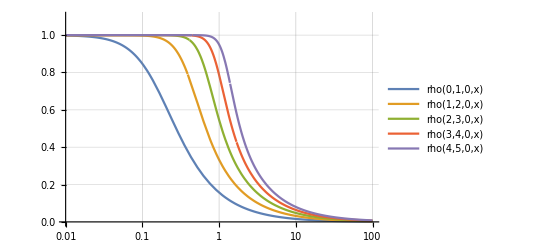

```mathematica
LogLinearPlot[{rho[0,1,0,x],rho[1,2,0,x],rho[2,3,0,x],rho[3,4,0,x],rho[4,5,0,x]},{x,0.01,100},PlotRange->{0,1.1},GridLines->Automatic,PlotLegends->"Expressions"]
```

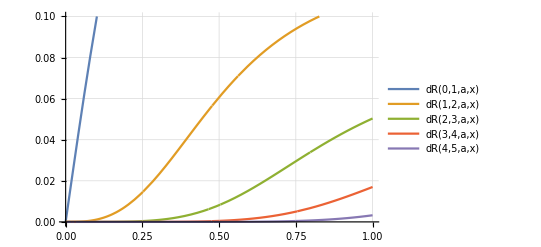

```mathematica
a=1/2;
Plot[{dR[0,1,a,x],dR[1,2,a,x],dR[2,3,a,x],dR[3,4,a,x],dR[4,5,a,x]},{x,0,1},PlotRange->{0,0.1},GridLines->Automatic,PlotLegends->"Expressions"]
```

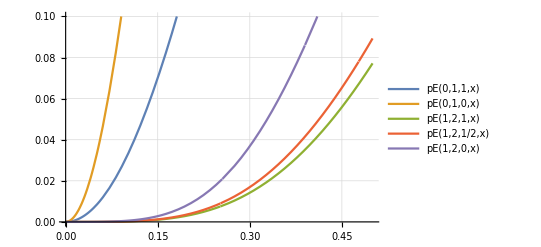

```mathematica
Plot[{pE[0,1,1,x],pE[0,1,0,x],pE[1,2,1,x],pE[1,2,1/2,x],pE[1,2,0,x]},{x,0,0.5},PlotRange->{0,0.1},GridLines->Automatic,PlotLegends->"Expressions"]
```

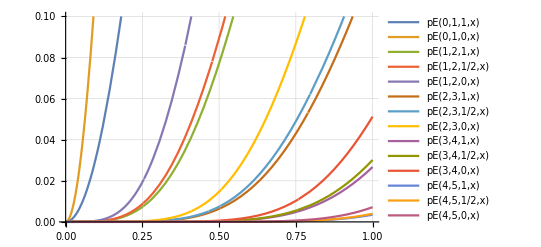

```mathematica
Plot[{pE[0,1,1,x],pE[0,1,0,x],pE[1,2,1,x],pE[1,2,1/2,x],pE[1,2,0,x],pE[2,3,1,x],pE[2,3,1/2,x],pE[2,3,0,x],pE[3,4,1,x],pE[3,4,1/2,x],pE[3,4,0,x],pE[4,5,1,x],pE[4,5,1/2,x],pE[4,5,0,x]},{x,0,1},PlotRange->{0,0.1},GridLines->Automatic,PlotLegends->"Expressions"]
```

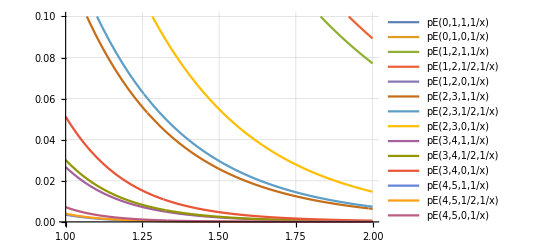

```mathematica
Plot[{pE[0,1,1,1/x],pE[0,1,0,1/x],pE[1,2,1,1/x],pE[1,2,1/2,1/x],pE[1,2,0,1/x],pE[2,3,1,1/x],pE[2,3,1/2,1/x],pE[2,3,0,1/x],pE[3,4,1,1/x],pE[3,4,1/2,1/x],pE[3,4,0,1/x],pE[4,5,1,1/x],pE[4,5,1/2,1/x],pE[4,5,0,1/x]},{x,1,2},PlotRange->{0,0.1},GridLines->Automatic,PlotLegends->"Expressions"]
```

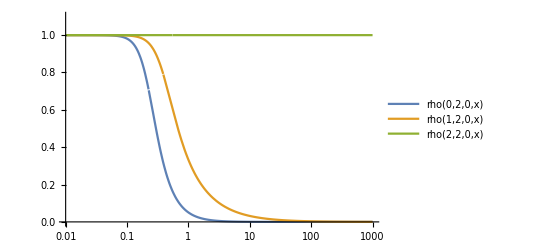

```mathematica
LogLinearPlot[{rho[0,2,0,x],rho[1,2,0,x],rho[2,2,0,x]},{x,0.01,1000},PlotRange->{0,1.1},PlotLegends->"Expressions"]
```

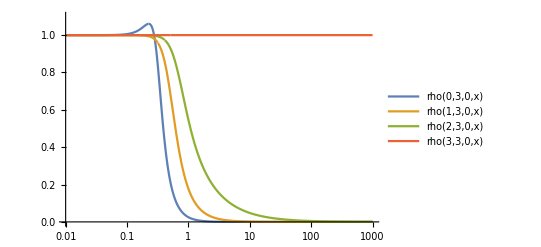

```mathematica
LogLinearPlot[{rho[0,3,0,x],rho[1,3,0,x],rho[2,3,0,x],rho[3,3,0,x]},{x,0.01,1000},PlotRange->{0,1.1},PlotLegends->"Expressions"]
```

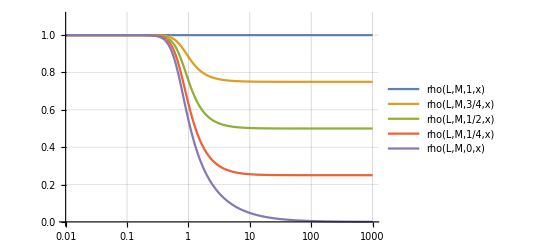

```mathematica
M=3; L=M-1;
LogLinearPlot[{rho[L,M,1,x],rho[L,M,3/4,x],rho[L,M,1/2,x], rho[L,M,1/4,x], rho[L,M,0,x]},{x,0.01,1000},PlotRange->{0,1.1},GridLines->Automatic,PlotLegends->"Expressions"]
```

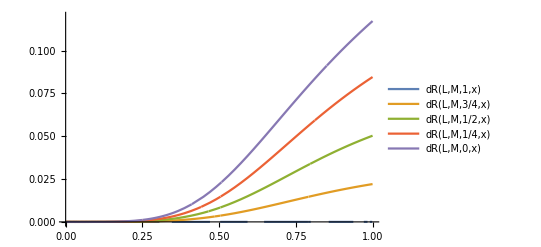

```mathematica
M=3; L=M-1;
Plot[{dR[L,M,1,x],dR[L,M,3/4,x],dR[L,M,1/2,x], dR[L,M,1/4,x], dR[L,M,0,x]},{x,0,1},PlotRange->{0,0.12},PlotLegends->"Expressions"]
```

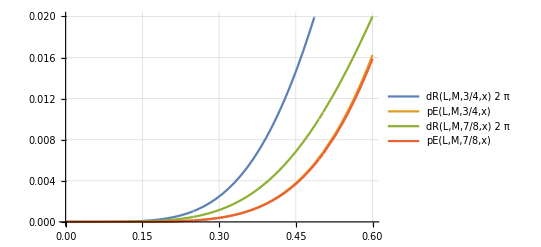

```mathematica
M=3; L=M-1;Plot[{dR[L,M,3/4,x]*2*Pi,pE[L,M,3/4,x],dR[L,M,7/8,x]*2*Pi,pE[L,M,7/8,x]},{x,0.0,0.6},PlotLegends->"Expressions",PlotRange->{0,0.02},GridLines->Automatic]
```

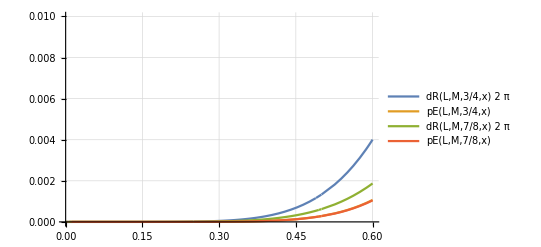

```mathematica
M=4; L=M-1;
Plot[{dR[L,M,3/4,x]*2*Pi,pE[L,M,3/4,x],dR[L,M,7/8,x]*2*Pi,pE[L,M,7/8,x]},{x,0.0,0.6},PlotLegends->"Expressions",PlotRange->{0,0.01},GridLines->Automatic]
```

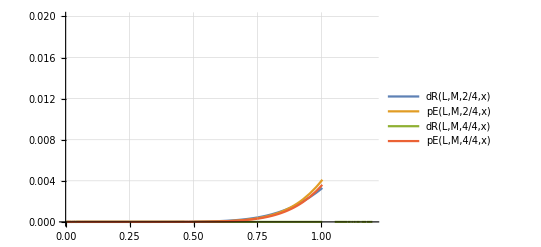

```mathematica
M=5;
L=M-1;
Plot[{dR[L,M,2/4,x],pE[L,M,2/4,x],dR[L,M,4/4,x],pE[L,M,4/4,x]},{x,0.0,1.2},PlotRange->{0,0.02},PlotLegends->"Expressions",GridLines->Automatic]
```

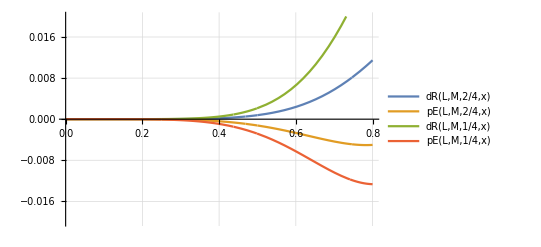

```mathematica
M=4;
L=M-2;
Plot[{dR[L,M,2/4,x],pE[L,M,2/4,x],dR[L,M,1/4,x],pE[L,M,1/4,x]},{x,0.0,0.8},PlotRange->{-0.02,0.02},PlotLegends->"Expressions",GridLines->Automatic]
```